## Naloga 1 (Polžek)

[20 točk] Sestavite funkcijo polzek[l_], kot je zapisano v navodilih.

```mathematica
polzek[l_]:=
```

```mathematica
polzek[{1,4,-1,-3,2}]//MatrixForm
```

(1 | 4 | -1
0 | 0 | -3
0 | 0 | 2)

```mathematica
polzek[{2,3,5,7,11,13,17,19,23,29,2,7}]//MatrixForm
```

(2 | 3 | 5 | 7
7 | 0 | 0 | 11
2 | 0 | 0 | 13
29 | 23 | 19 | 17)

```mathematica
polzek[{4,3,2,1}]//MatrixForm
```

(4 | 3
1 | 2)

```mathematica
polzek[{13}]//MatrixForm
```

(13)

[10 točk] Sestavite funkcijo odvij[l_], kot je zapisano v navodilih.

```mathematica
odvij[m_]:=
```

```mathematica
odvij[{{1,4,-1},{0,0,-3},{0,0,2}}]
```

{1,4,-1,-3,2,0,0,0,0}

```mathematica
odvij[{{2,3,5,7},{7,0,0,11},{2,0,0,13},{29,23,19,17}}]
```

{2,3,5,7,11,13,17,19,23,29,2,7,0,0,0,0}

```mathematica
odvij[{{4,3},{1,2}}]
```

{4,3,2,1}

```mathematica
odvij[{{13}}]
```

{13}

## Naloga 2 (Šestkotniki)

[30 točk] Sestavite funkcijo benz[l_], kot je zapisano v navodilih.

```mathematica
PolarToCartesian[{r_,fi_}]:={r*Cos[fi],r*Sin[fi]}
benz[l_]:=
```

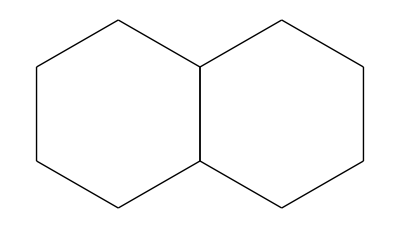

```mathematica
benz[{{-1,0},{0,0}}]
```

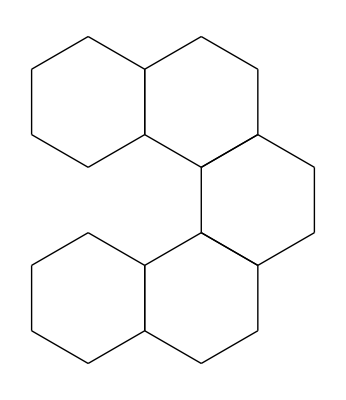

```mathematica
benz[{{0,0},{1,0},{1,1},{0,2},{-1,2}}]
```